```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
eqs=<<eqs.m;
eqsz0=<<eqsz0.m;
eqsz1=<<eqsz1.m;
jacobi=<<jacobi.m;
jacobiz0=<<jacobiz0.m;
jacobiz1=<<jacobiz1.m;
monitor=<<monitor.m;
(*Parameters*)
L=1;Lz=1.0;Lx=N[2π];
mu=1.4;mur=√(6-8 π L 0.043 mu);
Nz=20;Nx=40;Nzx=Nz*Nx;
Eye=IdentityMatrix[Nzx];Zero=ConstantArray[0,{Nzx,Nzx}];
```

## differential matrices and grid coordinates

```mathematica
(*Chebshev谱求导矩阵生成函数*)
chebp[n_]:=Table[Cos[(i π)/(n-1.0)],{i,0,n-1}];
cheb[n_,l_]:=Module[{x,c,sdm},x=chebp[n];c=Table[If[i==1||i==n,2.0,1.0],{i,1,n}];sdm=2/l Table[If[i≠j,c[[i]]/c[[j]](-1)^(i+j)/(x[[i]]-x[[j]]),0],{i,1,n},{j,1,n}];sdm-=DiagonalMatrix[Total[sdm,{2}]]];
dz=cheb[Nz,Lz];
dzs[0]=IdentityMatrix[Nz];dzs[1]=dz;dzs[2]=dz.dz;
gridz=0.5(chebp[Nz]+1);zz=gridz⊗ConstantArray[1,Nx];Z=Flatten[zz];
(*boundary index of holographic coordinate*)
z1=Flatten[Position[Z,n_/;n==gridz⟦1⟧]];z0=Flatten[Position[Z,n_/;n==gridz⟦-1⟧]];
zb=Join[z0,z1];
(*Fourier谱求导矩阵生成函数*)
fourier[n_,l_]:=π/l Table[If[i==j,0,(-1)^(i-j)If[Mod[n,2]==0,Cot[(π*(i-j))/n],Csc[(π*(i-j))/n]]],{i,1,n},{j,1,n}];
dx=fourier[Nx,Lx];
dxs[0]=IdentityMatrix[Nx];dxs[1]=dx;dxs[2]=dx.dx;
gridx=Lx/Nx Range[1,Nx];xx=ConstantArray[1,Nz]⊗gridx;X=Flatten[xx];
(*derivative matrix after vectorization*)
Do[If[i+j≤ 2,ds[i,j]=KroneckerProduct[dzs[i],dxs[j]]],{i,0,2},{j,0,2}];
```

## Newton-Kantorovich Method

```mathematica
(*Initialization & Descretization*)
a0=1.5;k0=2.0;
q1=s[Q1]=ConstantArray[1,Nzx];
q2=s[Q2]=ConstantArray[1,Nzx];
q3=s[Q3]=ConstantArray[0,Nzx];
q4=s[Q4]=ConstantArray[1,Nzx];
q5=s[Q5]=ConstantArray[1,Nzx];
q6=s[Q6]=0.1Cos[k0 X];
q7=s[Q7]=ConstantArray[mu,Nzx];
seed=Join[q1,q2,q3,q4,q5,q6,q7];
sol=seed;
ϵ=10^-10;k=0;kmax=9;normofsol={};normofeqs={};
While[Norm[sol,Infinity]>ϵ&&k<kmax,
diseqs=eqs/.{Derivative[i_,j_][h_][z,x]->ds[i,j].s[h],h_[z,x]->s[h],z->Z};
diseqsz0=eqsz0/.{Derivative[i_,j_][h_][z,x]:>(ds[i,j]⟦z0⟧).s[h],h_[z,x]:>s[h]⟦z0⟧,x:>X⟦z0⟧};
diseqsz1=eqsz1/.{Derivative[i_,j_][h_][z,x]:>(ds[i,j]⟦z1⟧).s[h],h_[z,x]:>s[h]⟦z1⟧};
diseqs⟦;;,z0⟧=diseqsz0;
diseqs⟦;;,z1⟧=diseqsz1;
b=-Flatten[diseqs];

J=jacobi/.{Derivative[i_,j_][h_][z,x]->ds[i,j].s[h],h_[z,x]->s[h],Subscript[d, i_,j_]->ds[i,j],eye->Eye,zero->Zero,z->Z};
Jz0=jacobiz0/.{Derivative[i_,j_][h_][z,x]:> (ds[i,j]⟦z0⟧).s[h],h_[z,x]:> s[h]⟦z0⟧,Subscript[d, i_,j_]:> ds[i,j]⟦z0⟧,eye:> Eye⟦z0⟧,zero:> Zero⟦z0⟧};
Jz1=jacobiz1/.{Derivative[i_,j_][h_][z,x]:> (ds[i,j]⟦z1⟧).s[h],h_[z,x]:> s[h]⟦z1⟧,Subscript[d, i_,j_]:> ds[i,j]⟦z1⟧,eye:> Eye⟦z1⟧,zero:> Zero⟦z1⟧};
J⟦;;,;;,z0⟧=Jz0;
J⟦;;,;;,z1⟧=Jz1;
J=ArrayFlatten[J];
sol=LinearSolve[J,b];
seed=seed+sol;
reseed=ArrayReshape[seed,{7,Nzx}];
q1=s[Q1]=reseed⟦1⟧;
q2=s[Q2]=reseed⟦2⟧;
q3=s[Q3]=reseed⟦3⟧;
q4=s[Q4]=reseed⟦4⟧;
q5=s[Q5]=reseed⟦5⟧;
q6=s[Q6]=reseed⟦6⟧;
q7=s[Q7]=reseed⟦7⟧;
k++;
(*Instant Inspection*)
AppendTo[normofsol,Norm[sol]];
AppendTo[normofeqs,Norm[b]];
Print["times of iteration: ",k];
Print["norm of sol: ",normofsol];
Print["norm of eqs: ",normofeqs];
Print["-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-"];
]//Timing
```

times of iteration: 1

norm of sol: {20.9}

norm of eqs: {323.371}

-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-

times of iteration: 2

norm of sol: {20.9,8.74414}

norm of eqs: {323.371,74.9602}

-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-

times of iteration: 3

norm of sol: {20.9,8.74414,1.16}

norm of eqs: {323.371,74.9602,14.2268}

-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-

times of iteration: 4

norm of sol: {20.9,8.74414,1.16,0.046943}

norm of eqs: {323.371,74.9602,14.2268,1.20065}

-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-

times of iteration: 5

norm of sol: {20.9,8.74414,1.16,0.046943,0.000243661}

norm of eqs: {323.371,74.9602,14.2268,1.20065,0.0112846}

-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-

times of iteration: 6

norm of sol: {20.9,8.74414,1.16,0.046943,0.000243661,6.3974×10^-9}

norm of eqs: {323.371,74.9602,14.2268,1.20065,0.0112846,4.52314×10^-7}

-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-

times of iteration: 7

norm of sol: {20.9,8.74414,1.16,0.046943,0.000243661,6.3974×10^-9,2.01754×10^-12}

norm of eqs: {323.371,74.9602,14.2268,1.20065,0.0112846,4.52314×10^-7,7.41258×10^-11}

-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-*-

{37.5781,Null}

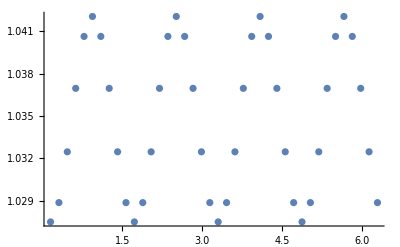

-Graphics3D-

-Graphics3D-

-Graphics3D-

«4 more identical outputs»

```mathematica
gridx=Reverse[gridx];
solq1=ArrayReshape[q1,{Nz,Nx}];
solq2=ArrayReshape[q2,{Nz,Nx}];
solq3=ArrayReshape[q3,{Nz,Nx}];
solq4=ArrayReshape[q4,{Nz,Nx}];
solq5=ArrayReshape[q5,{Nz,Nx}];
solq6=ArrayReshape[q6,{Nz,Nx}];
solq7=ArrayReshape[q7,{Nz,Nx}];
density=mu-dz⟦-1⟧.solq7;
ListPlot[Table[{gridx⟦i⟧,density⟦i⟧},{i,1,Nx}],PlotRange->All]
ListPlot3D[Flatten[Table[{gridz⟦i⟧,gridx⟦j⟧,solq1⟦i,j⟧},{i,Nz},{j,Nx}],1],PlotRange->All]
ListPlot3D[Flatten[Table[{gridz⟦i⟧,gridx⟦j⟧,solq2⟦i,j⟧},{i,Nz},{j,Nx}],1],PlotRange->All]
ListPlot3D[Flatten[Table[{gridz⟦i⟧,gridx⟦j⟧,solq3⟦i,j⟧},{i,Nz},{j,Nx}],1],PlotRange->All]
ListPlot3D[Flatten[Table[{gridz⟦i⟧,gridx⟦j⟧,solq4⟦i,j⟧},{i,Nz},{j,Nx}],1],PlotRange->All]
ListPlot3D[Flatten[Table[{gridz⟦i⟧,gridx⟦j⟧,solq5⟦i,j⟧},{i,Nz},{j,Nx}],1],PlotRange->All]
ListPlot3D[Flatten[Table[{gridz⟦i⟧,gridx⟦j⟧,solq6⟦i,j⟧},{i,Nz},{j,Nx}],1],PlotRange->All]
ListPlot3D[Flatten[Table[{gridz⟦i⟧,gridx⟦j⟧,solq7⟦i,j⟧},{i,Nz},{j,Nx}],1],PlotRange->All]
```

```mathematica
submonitor=monitor/.{Derivative[i_,j_][h_][z,x]->ds[i,j].s[h],h_[z,x]->s[h],z->Z};
submonitor⟦zb⟧=0;
Norm[submonitor]
```

Power::infy: 碰到无穷表达式 1/0.^2.

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

Infinity::indet: 碰到不定表达式 0. ComplexInfinity.

General::stop: 在本次计算中，Infinity::indet 的进一步输出将被抑制.

1.11435×10^-9

```mathematica
MatrixPlot[J]
```

-Graphics-